```mathematica
A=2.794564397672058e-13;
B=105782.64917210047;
Const=2.3238013019071064;
```

```mathematica
Δ[I0_,t_]:=FindRoot[(1+I0) Delt+1/3 Delt^3==B I0 t,{Delt,0}]
v[I0_,t_]:=Delt*Const/.Δ[I0,t]
```

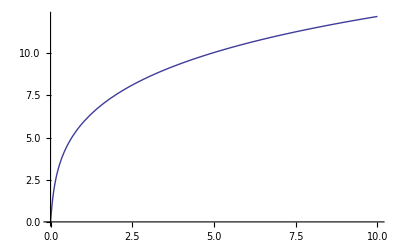

```mathematica
Plot[v[inot,0.0001],{inot,0,10}]
```

```mathematica
Vat100us=Table[{v[i/10,0.0001],N[i/10]},{i,0,100}];
Export["C:\\Python27\\Imaging Model\\Mathematica_100us.dat",Vat100us]
```

C:\Python27\Imaging Model\Mathematica_100us.dat

```mathematica
Vat50us=Table[{v[i/10,0.00005],N[i/10]},{i,0,100}];
Export["C:\\Python27\\Imaging Model\\Mathematica_50us.dat",Vat50us]
```

C:\Python27\Imaging Model\Mathematica_50us.dat

```mathematica
Vat10us=Table[{v[i/10,0.00001],N[i/10]},{i,0,100}];
Export["C:\\Python27\\Imaging Model\\Mathematica_10us.dat",Vat10us]
```

C:\Python27\Imaging Model\Mathematica_10us.dat